```mathematica
Slider2D[Dynamic[{y0,z0}],{-2,2}]
```

```mathematica
a=-0.7; b = 0.8; tau = 1/0.08;tm = 100;
```

```mathematica
c[t_] := N[Exp[-(t-10)^2] + 200*Exp[-(t-30)^2]^2+ Exp[-(t-70)^2]]
```

```mathematica
eq1 = y'[t] == y[t]-y[t]^3-z[t]+c[t];
eq2 =  z'[t] == (y[t] - a - b*z[t]) / tau;
```

```mathematica
Dynamic[Plot[Evaluate[y[t] /. NDSolve[{eq1,eq2, y[0]==y0, z[0]==z0} ,{y,z},{t,0,101}],{t,0,100},PlotRange->{{0,tm},{-1.5,1.5}}]]]
```

```mathematica
{Dynamic[y0], Dynamic[z0]}
```

{,}

```mathematica
c[2]
```

1/e^64

```mathematica
numeric
```

```mathematica
Exp[2]
```

ⅇ^2

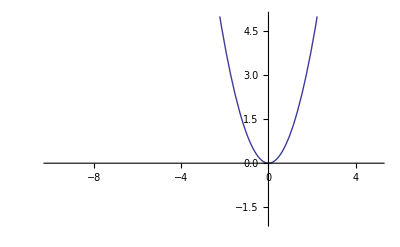

```mathematica
Plot[x^2,{x,-5,5},PlotRange->{{-10,5},{-2,5}}]
```